Analytic Scalar Charges in Scalar-Tensor Theory

Date: 	April 2021

Authors: 	Kent Yagi
		Michael Stepniczka

Reference: Yagi & Stepniczka  arXiv: 2105.01614

Note: 	We suppress the expressions since they are lengthy.

### Loading mx file

```mathematica
SetDirectory[NotebookDirectory[]];
<<scalar_charges.mx
```

### Example Values for Parameters

```mathematica
α0Test=10^-5;
β0Test1=-4.2;
β0Test2=-4.5;
CATestTol=0.22;
CATestCD=0.27;
```

## Tolman VII

### Perturbative Scalar Charge

α_A(C_A; α_0,β_0)
given as a 5th order Pade approximant in terms of C_A

```mathematica
αAPertTol;
```

#### Example Value

```mathematica
αAPertTol/.{α0->α0Test,β0->β0Test1,CA->CATestTol}
```

0.000159923

#### Example Plot (α_0=10^-5)

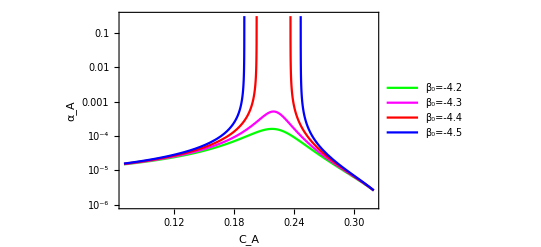

```mathematica
plotPertTol=LogPlot[{αAPertTol/.{α0->α0Test,β0->-4.2},αAPertTol/.{α0->α0Test,β0->-4.3},αAPertTol/.{α0->α0Test,β0->-4.4},αAPertTol/.{α0->α0Test,β0->-4.5}},{CA,0.07,0.32},PlotLegends->{"β_0=-4.2","β_0=-4.3","β_0=-4.4","β_0=-4.5"},FrameLabel->{"C_A","α_A"},PlotStyle->{Green,Magenta,Red,Blue},Frame->True,PlotRange->{{0.07,0.32},{10^-6,0.3}}]
```

### Spontaneous Scalar Charge

α_0=0

#### d_1, d_2, e_1 coefficients

α_0 = d_1 α_c + d_2 α_c^3 + O(α_c^5)
α_A = e_1 α_c + O(α_c^3)
each coefficient is a function of C_A and β_0, given as a 4 th order Pade approximant in terms of C_A

```mathematica
d1Tol;
d2Tol;
e1Tol;
```

#### Spontaneous Scalar Charge

α_A(C_A; β_0)

```mathematica
αASpntTol=√(-d1/d2)e1/.{d1->d1Tol,d2->d2Tol,e1->e1Tol};
```

#### Example Value

```mathematica
αASpntTol/.{β0->β0Test2,CA->CATestTol}
```

0.233091

#### Example Plot (α_0=10^-5)

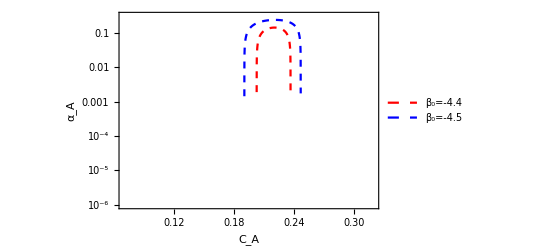

```mathematica
plotSpntTol=LogPlot[{αASpntTol/.{α0->α0Test,β0->-4.4},αASpntTol/.{α0->α0Test,β0->-4.5}},{CA,0.07,0.32},PlotLegends->{"β_0=-4.4","β_0=-4.5"},FrameLabel->{"C_A","α_A"},PlotStyle->{{Red,Dashed},{Blue,Dashed}},Frame->True,PlotRange->{{0.07,0.32},{10^-6,0.3}}]
```

combined plot

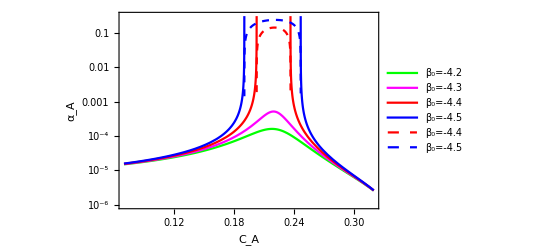

```mathematica
Show[plotPertTol,plotSpntTol]
```

## Constant Density Stars

### Perturbative Scalar Charge

α_A(C_A; α_0,β_0)
given as a 5th order Pade approximant in terms of C_A

```mathematica
αAPertCD;
```

#### Example Value

```mathematica
αAPertCD/.{α0->α0Test,β0->β0Test1,CA->CATestCD}
```

0.000163932

#### Example Plot (α_0=10^-5)

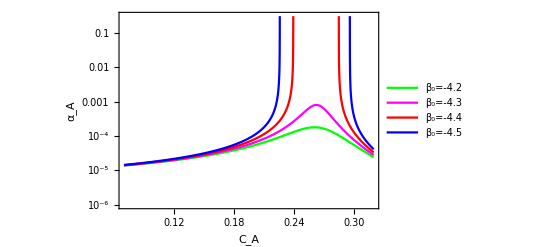

```mathematica
plotPertCD=LogPlot[{αAPertCD/.{α0->α0Test,β0->-4.2},αAPertCD/.{α0->α0Test,β0->-4.3},αAPertCD/.{α0->α0Test,β0->-4.4},αAPertCD/.{α0->α0Test,β0->-4.5}},{CA,0.07,0.32},PlotLegends->{"β_0=-4.2","β_0=-4.3","β_0=-4.4","β_0=-4.5"},FrameLabel->{"C_A","α_A"},PlotStyle->{Green,Magenta,Red,Blue},Frame->True,PlotRange->{{0.07,0.32},{10^-6,0.3}}]
```

### Spontaneous Scalar Charge

α_0=0

#### d_1, d_2, e_1 coefficients

α_0 = d_1 α_c + d_2 α_c^3 + O(α_c^5)
α_A = e_1 α_c + O(α_c^3)
each coefficient is a function of C_A and β_0, given as a 4 th order Pade approximant in terms of C_A

```mathematica
d1CD;
d2CD;
e1CD;
```

#### Spontaneous Scalar Charge

α_A(C_A; β_0)

```mathematica
αASpntCD=√(-d1/d2)e1/.{d1->d1CD,d2->d2CD,e1->e1CD};
```

#### Example Value

```mathematica
αASpntCD/.{β0->β0Test2,CA->CATestCD}
```

0.240134

#### Example Plot (α_0=10^-5)

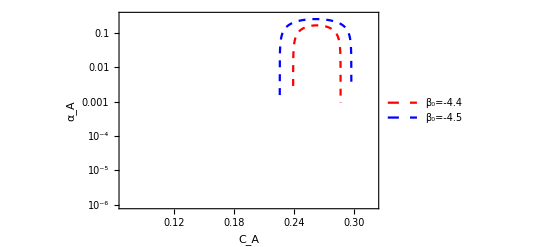

```mathematica
plotSpntCD=LogPlot[{αASpntCD/.{α0->α0Test,β0->-4.4},αASpntCD/.{α0->α0Test,β0->-4.5}},{CA,0.07,0.32},PlotLegends->{"β_0=-4.4","β_0=-4.5"},FrameLabel->{"C_A","α_A"},PlotStyle->{{Red,Dashed},{Blue,Dashed}},Frame->True,PlotRange->{{0.07,0.32},{10^-6,0.3}}]
```

combined plot

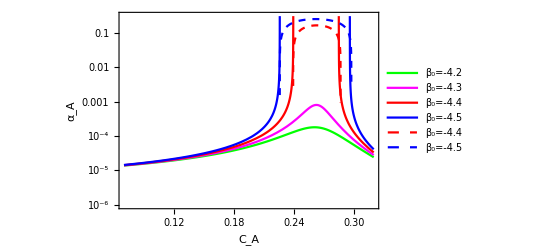

```mathematica
Show[plotPertCD,plotSpntCD]
```